```mathematica
UserDirectory=ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]
SetDirectory[UserDirectory] 
(* list of files with extension asc *) 
filesASC=FileNames["*.asc"]
(* no data value for the raster *) 
NoDataValue=1400;
```

D:\Donnees_RAMMS_Chumma\

D:\Donnees_RAMMS_Chumma

{p100s130_21_MaxHeight.asc,p100s130_21_MaxVelocity.asc}

## Raster with xmin, ymin, nrow, ncol

```mathematica
(* reading the raster in the ESRI ASCII form and determining the geoparameters *) 
(*data=ReadList["topo5m.asc",String,RecordLists->True];*)
data=ReadList["dem\a10037.txt",String,RecordLists->True];
dim= Length@data;

ymin=StringCases[data[[4,1]],x:NumberString:>ToExpression[x]][[1]];
xmin=StringCases[data[[3,1]],x:NumberString:>ToExpression[x]][[1]];
 ny=StringCases[data[[2,1]],x:NumberString:>ToExpression[x]][[1]];
 nx=StringCases[data[[1,1]],x:NumberString:>ToExpression[x]][[1]];
ndata={};
Do[AppendTo[ndata,Flatten@ToExpression@StringSplit[data[[i,1]]," "]],{i,7,dim}]
pasX=StringCases[data[[5,1]],x:NumberString:>ToExpression[x]][[1]];
pasY=StringCases[data[[5,1]],x:NumberString:>ToExpression[x]][[1]];

newdata=Replace[ndata,Except[_?NumericQ]->NoDataValue,{2}];
Dimensions@newdata
Dimensions@ndata
```

ReadList::noopen: Cannot open topo5m.asc.

{1051,1362}

{1051,1362}

```mathematica
(* plot the DEM *) 
tableau=Flatten[Table[{xmin+(i-1) pasX,ymin+(ny-k+1) pasX,newdata[[k,i]]},{i,nx},{k,ny}],1];
fnc=Interpolation[tableau];
{{XImin,XImax},{YImin,YImax}}=ReleaseHold@Extract[fnc,1,Hold];
zmin=Min[#[[3]]&/@tableau];
zmax=Max[#[[3]]&/@tableau];
vue=ContourPlot[fnc[x,y],{x,XImin,XImax},{y,YImin,YImax},Contours->Range[zmin,zmax,10], AspectRatio->(YImax-ymin)/(XImax-xmin) ]
```

-Graphics-

```mathematica
(* export the DEM in the format desired by clawpack *) 

ndata2=Flatten[newdata,1];
ndata2//Dimensions
 
fileExport=OpenWrite["topo.asc",FormatType->OutputForm,PageWidth->Infinity];
Write[fileExport,"ncols        ",nx];
Write[fileExport,"nrows        ",ny];
Write[fileExport,"xllcorner    ",Ceiling[xmin]];
Write[fileExport,"yllcorner    ",Ceiling[ymin]];
Write[fileExport,"cellsize     ",pasX];
Write[fileExport,"nodata_value ",NoDataValue];
Do[
Write[fileExport,ndata2[[i]]],
{i,  Length@ndata2}]//Timing
Close[fileExport]
```

{1431462}

{4.47723,Null}

topo.asc

## Starting area export

```mathematica
(* list of shapefiles *) 
filesSHP=FileNames["*.shp"]
(* initial snow depth *) 
ICDepth=2.;
(* initial velocity -- for future use (not used for now) *) 
ICVelocity=0.;
```

{P.shp}

```mathematica
(* import the shapefile of the starting area *) 
data=Import["P.shp","Data"] 
data2=(("Geometry"/.data) /.Polygon[x__]->x)[[1]] ;
poly=data2[[1]];
Length[poly];
```

{{LayerName→P,Geometry→{Polygon[…]},Labels→{Id},LabeledData→{Id→{0}}}}

```mathematica
file={};
xpmin=Min[#[[1]]&/@poly]
ypmin=Min[#[[2]]&/@poly]
xpmax=Max[#[[1]]&/@poly]
ypmax=Max[#[[2]]&/@poly]
status=0;
ProgressIndicator[Dynamic[status]]
Do[status= k /ny;
Do[

pt={xmin+(i-1)pasX,ymin+(ny-k+1) pasY};
If[xpmin≤ pt[[1]]≤ xpmax && ypmin≤ pt[[2]]≤ ypmax, 
If[RegionMember[Polygon@poly,pt],
AppendTo[file,{ToString[AccountingForm@pt[[1]]]," ",ToString[AccountingForm@pt[[2]]], " ",ICDepth }],
AppendTo[file,{ToString[AccountingForm@pt[[1]]], " ",ToString[AccountingForm@pt[[2]]], " ",0. }]
],
AppendTo[file,{ToString[AccountingForm@pt[[1]]], " ",ToString[AccountingForm@pt[[2]]], " ",0. }]]
, {i,nx}],
{k,ny} ]//Timing
Close[fileExport]
```

2.62737×10^6

1.09847×10^6

2.62761×10^6

1.09861×10^6

{13514.5,Null}

Close[OutputStream[initial.xyz,3]]

```mathematica
file//Length
```

1431462

```mathematica
Export["file.dat",file]
```

file.dat

## Check

```mathematica
(* check whether the points lie in the right area *) 
pts={};

Do[
Do[
pt={xmin+(i-1)pasX,ymin+(ny-k+1) pasY};
If[RegionMember[Polygon@poly,pt],
AppendTo[pts,{Red,Point[pt]}]

]
, {i,nx}],
{k,ny} ]//Timing
```

{154.067,Null}

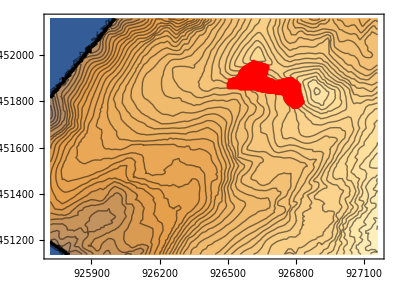

```mathematica
Show[vue,Graphics@Line[poly],Graphics@pts,PlotRange->All]
```